```mathematica
PlotList[lis_]:=Table[
Graphics[
{Blend[{White,Black},.5(1+lis[[i,3]])],PointSize[0.04],Point[{lis[[i,2]],lis[[i,1]]}]
}
],
{i,Length@lis}]//Show[#,AspectRatio->1]&
PlotList1[lis_]:=Table[
Graphics3D[
{Blend[{White,Black},.5(1+lis[[i,3]])],PointSize[0.04],Point[{Sin[lis[[i,1]]]Cos[lis[[i,2]]],Sin[lis[[i,1]]]Sin[lis[[i,2]]],Cos[lis[[i,1]]]}]
}
],
{i,Length@lis}]//Show[#,AspectRatio->1]&
```

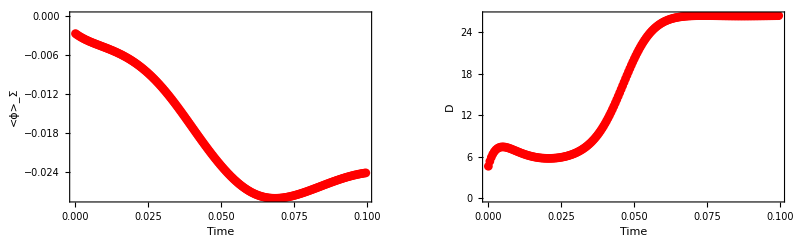

```mathematica
nofFiles=Length@FileNames["s-t*.dat",NotebookDirectory[]][[;;]];δplots=Round[(nofFiles-1)/15];
hiList=Import[ToString[NotebookDirectory[]]<>"hi.dat"];
GraphicsRow[{ListPlot[hiList[[;;,{1,2}]],Frame->True,Axes->False,FrameStyle->Large,ImageSize->1000,Joined->True,PlotStyle->Red,PlotMarkers->{"•", 9},FrameLabel-> {"Time","<ϕ>_Σ"}],
ListPlot[hiList[[;;,{1,3}]],Frame->True,Axes->False,FrameStyle->Large,ImageSize->1000,Joined->True,PlotStyle->Red,PlotMarkers->{"•", 9},FrameLabel-> {"Time","D"}]},ImageSize->Full]
```

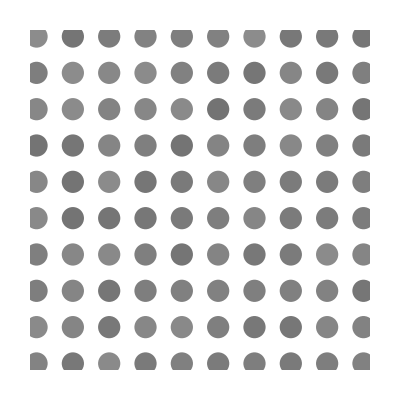
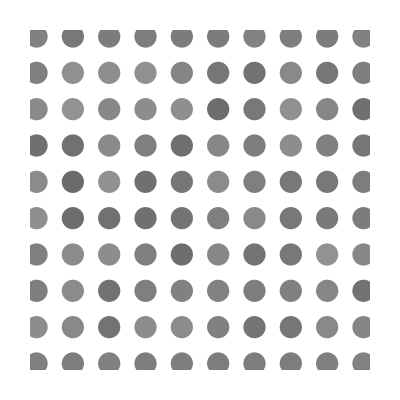
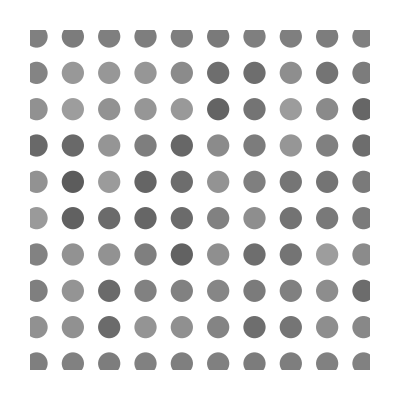
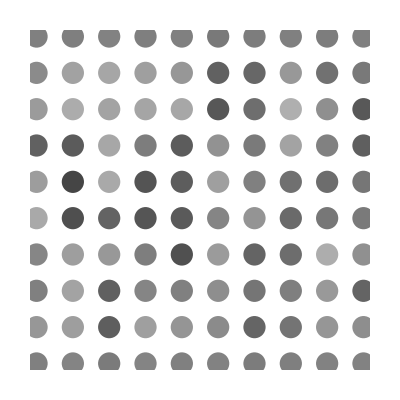
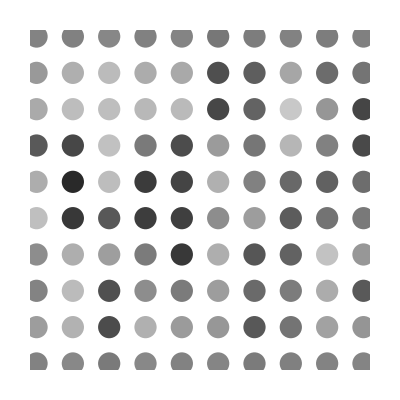
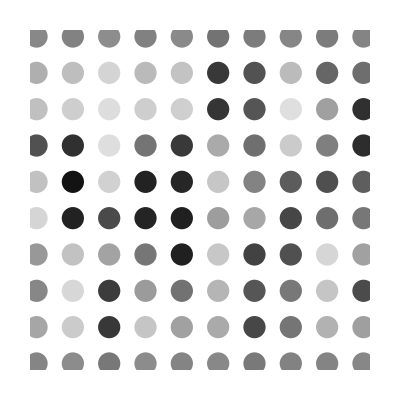
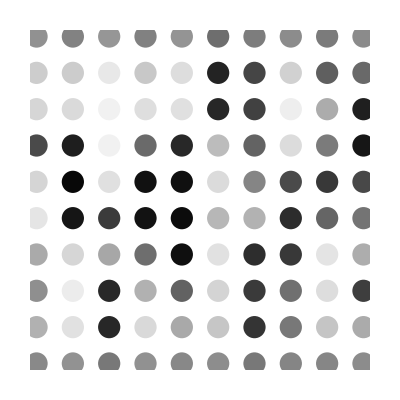
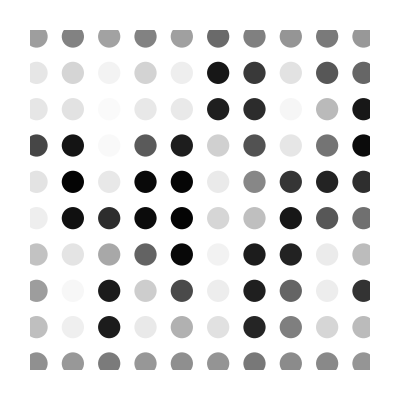

```mathematica
Table[PlotList[Import[ToString[NotebookDirectory[]]<>"s-t"<>ToString[i]<>".dat"]],{i,0,nofFiles,δplots}]
```

```mathematica
Table[PlotList1[Import[ToString[NotebookDirectory[]]<>"s-t"<>ToString[i]<>".dat"]],{i,0,nofFiles,δplots}]
```

{-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-}

```mathematica
Sum[Sin[(i-1/2) Δθ]Δθ,{i,1,Nθ}]/.Δθ->π/Nθ/.Nθ->1000//N
```

2.